```mathematica
Needs["GREATER2`"];
```

w::shdw: Symbol w appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

z::shdw: Symbol z appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

x::shdw: Symbol x appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

i::shdw: Symbol i appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

j::shdw: Symbol j appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

a::shdw: Symbol a appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

c::shdw: Symbol c appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

m::shdw: Symbol m appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

n::shdw: Symbol n appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

p::shdw: Symbol p appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

q::shdw: Symbol q appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

p$::shdw: Symbol p$ appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

f::shdw: Symbol f appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

v::shdw: Symbol v appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

V::shdw: Symbol V appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

g::shdw: Symbol g appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

ru::shdw: Symbol ru appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

t::shdw: Symbol t appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

y::shdw: Symbol y appears in multiple contexts {GREATER2`,Global`}; definitions in context GREATER2` may shadow or be shadowed by other definitions.

GREATER has been loaded. Some functions = antisymmetrize, CoD (covariant derivative), Contract, ds2met (covert line element to metric), Epsilon, KillingEquations, SimpleDeriv (partial derivative), LieD (Lie derivative), ChangeCoords, DAlembertian , FieldStrength (F = dA), IndexShift, symmetrize, TJacobian, Trans2rules, SelfContract, CottonTensor, wedge, ExtrinsicCurvature, ShowComponents

```mathematica
Hcbm=67.4
```

67.4

```mathematica
Hsnova=74.8
k=Sqrt[1-(Hcbm/Hsnova)^2]
```

74.8

0.433675

```mathematica
Clear[G,c]
```

```mathematica
(* define our coordinates *)
X =  {t,τ,r,ϕ,θ};
```

```mathematica
(* define a line element Robertson-Walker metric on anti-deSitter *)
ds2 =  c^2*dt^2+c^2*dτ^2 -( dr^2/((1-k^2*r^2 )*(1-r^2))+ r^2 dϕ^2+r^2*Sin[ϕ]^2dθ^2);
```

```mathematica
(* calculate metric tensor*)
gdd = Metric[ds2, X]
```

{{c^2,0,0,0,0},{0,c^2,0,0,0},{0,0,-5.31706/(5.31706-6.31706 r^2+1. r^4),0,0},{0,0,0,-r^2,0},{0,0,0,0,-r^2 Sin[ϕ]^2}}

```mathematica
TableForm[gdd]
```

c^2 | 0 | 0 | 0 | 0
0 | c^2 | 0 | 0 | 0
0 | 0 | -5.31706/(5.31706-6.31706 r^2+1. r^4) | 0 | 0
0 | 0 | 0 | -r^2 | 0
0 | 0 | 0 | 0 | -r^2 Sin[ϕ]^2

```mathematica
Det[gdd]
```

-(5.31706 c^4 r^4 Sin[ϕ]^2)/(5.31706-6.31706 r^2+1. r^4)

```mathematica
Tr[gdd]
```

2 c^2-r^2-5.31706/(5.31706-6.31706 r^2+1. r^4)-r^2 Sin[ϕ]^2

```mathematica
(* inverse metric of metric tensor *)
guu =IMetric[gdd];
```

```mathematica
TableForm[guu]
```

1./c^2 | 0. | 0. | 0. | 0.
0. | 1./c^2 | 0. | 0. | 0.
0. | 0. | -1.+1.18807 r^2-0.188074 r^4 | 0. | 0.
0. | 0. | 0. | -1./r^2 | 0.
0. | 0. | 0. | 0. | -(1. Csc[ϕ]^2)/r^2

```mathematica
Det[guu]
```

0.-(0.188074 Csc[ϕ]^2)/c^4-(1. Csc[ϕ]^2)/(c^4 r^4)+(1.18807 Csc[ϕ]^2)/(c^4 r^2)

```mathematica
Tr[guu]
```

-1.+2./c^2-1./r^2+1.18807 r^2-0.188074 r^4-(1. Csc[ϕ]^2)/r^2

```mathematica
(*Compute the Ricci scalar *)
Rs = SCurvature[gdd, X]
```

(1.-7.12844 r^2+1.88074 r^4+1. Cot[ϕ]^2-1. Csc[ϕ]^2)/r^2

```mathematica
(* Gaussian curvature:*)
K=Tr[ExtrinsicCurvature[gdd,3, 1, X]]
```

0.-1. (0.+(1. (1. r-1.18807 r^3+0.188074 r^5))/(√(-1.+1.18807 r^2-0.188074 r^4)))-(0.+(-1.+1.18807 r^2-0.188074 r^4) (-1/(-1.+1.18807 r^2-0.188074 r^4)-5.31706/(5.31706-6.31706 r^2+1. r^4))) (0.+((-4.7225×10^-15 r+1.889×10^-14 r^3) (0.+(-1.+1.18807 r^2-0.188074 r^4) (-1/(-1.+1.18807 r^2-0.188074 r^4)-5.31706/(5.31706-6.31706 r^2+1. r^4))))/(√(-1.+1.18807 r^2-0.188074 r^4) (5.31706-6.31706 r^2+1. r^4)^2))-1. (0.-1. r √(-1.+1.18807 r^2-0.188074 r^4) Sin[ϕ]^2)

```mathematica
(* calcxulate full Riemann Curvature tensor*)
Rhijk=Riemann[guu,X];
TableForm[FullSimplify[ExpandAll[Rhijk]]]
```

0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.-26.5853/(28.2712-67.1765 r^2+50.5394 r^4-12.6341 r^6+1. r^8)+(-84.8135+134.353 r^2)/(r^4 (28.2712-67.1765 r^2+50.5394 r^4-12.6341 r^6+1. r^8))+5.31706/(5.31706 r^4-6.31706 r^6+1. r^8) | 0.
0. | 0. | 0.+26.5853/(28.2712-67.1765 r^2+50.5394 r^4-12.6341 r^6+1. r^8)+(84.8135-134.353 r^2)/(r^4 (28.2712-67.1765 r^2+50.5394 r^4-12.6341 r^6+1. r^8))-5.31706/(5.31706 r^4-6.31706 r^6+1. r^8) | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | ((-56.5423+100.765 r^2-21.2683 r^4) Csc[ϕ]^2)/(r^4 (28.2712-67.1765 r^2+50.5394 r^4-12.6341 r^6+1. r^8))
0. | 0. | 0. | 0. | 0.
0. | 0. | ((56.5423-100.765 r^2+21.2683 r^4) Csc[ϕ]^2)/(r^4 (28.2712-67.1765 r^2+50.5394 r^4-12.6341 r^6+1. r^8)) | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.+2./r^2-6.31706/(5.31706-6.31706 r^2+1. r^4)+(2. r^2)/(5.31706-6.31706 r^2+1. r^4) | 0.
0. | 0. | 0.-2./r^2+6.31706/(5.31706-6.31706 r^2+1. r^4)-(2. r^2)/(5.31706-6.31706 r^2+1. r^4) | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | Csc[ϕ]^2 (-5.31706/(5.31706 r^4-6.31706 r^6+1. r^8)-1. Cot[ϕ]^2-1. Csc[ϕ]^2)
0. | 0. | 0. | Csc[ϕ]^2 (5.31706/(5.31706 r^4-6.31706 r^6+1. r^8)+1. Cot[ϕ]^2+1. Csc[ϕ]^2) | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.+2./r^2-6.31706/(5.31706-6.31706 r^2+1. r^4)+(2. r^2)/(5.31706-6.31706 r^2+1. r^4)
0. | 0. | 0. | 0. | 0.
0. | 0. | 0.-2./r^2+6.31706/(5.31706-6.31706 r^2+1. r^4)-(2. r^2)/(5.31706-6.31706 r^2+1. r^4) | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 5.31706/(5.31706 r^4-6.31706 r^6+1. r^8)+1. Cot[ϕ]^2+1. Csc[ϕ]^2
0. | 0. | 0. | -5.31706/(5.31706 r^4-6.31706 r^6+1. r^8)-1. Cot[ϕ]^2-1. Csc[ϕ]^2 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.

```mathematica
(* Ricci tensor contraction*)
Rij=FullSimplify[ExpandAll[TensorContract[TensorTranspose[Rhijk,{4,1,2,3}],{2,1}]]]
```

{{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,(300.639-892.954 r^2+806.164 r^4-235.118 r^6+21.2683 r^8+(300.639-892.954 r^2+806.164 r^4-235.118 r^6+21.2683 r^8) Csc[ϕ]^2)/(r^4 (150.32-535.772 r^2+721.351 r^4-453.614 r^6+135.667 r^8-18.9512 r^10+1. r^12)),0.,0.},{0.,0.,0.,(10.6341 r^2-18.9512 r^4+4. r^6+5.31706 Csc[ϕ]^2+r^4 (7.9756-9.4756 r^2+1.5 r^4+(2.65853-3.15853 r^2+0.5 r^4) Cos[2 ϕ]) Csc[ϕ]^4)/(r^4 (5.31706-6.31706 r^2+1. r^4)),0.},{0.,0.,0.,0.,1. Cot[ϕ]^2+(5.31706+10.6341 r^2-18.9512 r^4+4. r^6+r^4 (5.31706-6.31706 r^2+1. r^4) Csc[ϕ]^2)/(r^4 (5.31706-6.31706 r^2+1. r^4))}}

```mathematica
Tr[Rij]
```

0.+1. Cot[ϕ]^2+(5.31706+10.6341 r^2-18.9512 r^4+4. r^6+r^4 (5.31706-6.31706 r^2+1. r^4) Csc[ϕ]^2)/(r^4 (5.31706-6.31706 r^2+1. r^4))+(300.639-892.954 r^2+806.164 r^4-235.118 r^6+21.2683 r^8+(300.639-892.954 r^2+806.164 r^4-235.118 r^6+21.2683 r^8) Csc[ϕ]^2)/(r^4 (150.32-535.772 r^2+721.351 r^4-453.614 r^6+135.667 r^8-18.9512 r^10+1. r^12))+(10.6341 r^2-18.9512 r^4+4. r^6+5.31706 Csc[ϕ]^2+r^4 (7.9756-9.4756 r^2+1.5 r^4+(2.65853-3.15853 r^2+0.5 r^4) Cos[2 ϕ]) Csc[ϕ]^4)/(r^4 (5.31706-6.31706 r^2+1. r^4))

```mathematica
G=6.732*10^(-8);
c=2.997925*10^(10);
hbar=1.05457266*10^(-27);
```

```mathematica
mplanck=Sqrt[hbar*c/G];
```

```mathematica
(* the Einstein energy density equation without cosmological constant*)
Tij=(-c^5/(4*Pi^2*G^(5/4)*Sqrt[5]))*(Rij-guu*Rs/2)
```

{{-2.52976×10^59 (0.-(5.56325×10^-22 (1.-7.12844 r^2+1.88074 r^4+1. Cot[ϕ]^2-1. Csc[ϕ]^2))/r^2),0.,0.,0.,0.},{0.,-2.52976×10^59 (0.-(5.56325×10^-22 (1.-7.12844 r^2+1.88074 r^4+1. Cot[ϕ]^2-1. Csc[ϕ]^2))/r^2),0.,0.,0.},{0.,0.,-2.52976×10^59 (-((-1.+1.18807 r^2-0.188074 r^4) (1.-7.12844 r^2+1.88074 r^4+1. Cot[ϕ]^2-1. Csc[ϕ]^2))/(2 r^2)+(300.639-892.954 r^2+806.164 r^4-235.118 r^6+21.2683 r^8+(300.639-892.954 r^2+806.164 r^4-235.118 r^6+21.2683 r^8) Csc[ϕ]^2)/(r^4 (150.32-535.772 r^2+721.351 r^4-453.614 r^6+135.667 r^8-18.9512 r^10+1. r^12))),0.,0.},{0.,0.,0.,-2.52976×10^59 ((0.5 (1.-7.12844 r^2+1.88074 r^4+1. Cot[ϕ]^2-1. Csc[ϕ]^2))/r^4+(10.6341 r^2-18.9512 r^4+4. r^6+5.31706 Csc[ϕ]^2+r^4 (7.9756-9.4756 r^2+1.5 r^4+(2.65853-3.15853 r^2+0.5 r^4) Cos[2 ϕ]) Csc[ϕ]^4)/(r^4 (5.31706-6.31706 r^2+1. r^4))),0.},{0.,0.,0.,0.,-2.52976×10^59 (1. Cot[ϕ]^2+(0.5 Csc[ϕ]^2 (1.-7.12844 r^2+1.88074 r^4+1. Cot[ϕ]^2-1. Csc[ϕ]^2))/r^4+(5.31706+10.6341 r^2-18.9512 r^4+4. r^6+r^4 (5.31706-6.31706 r^2+1. r^4) Csc[ϕ]^2)/(r^4 (5.31706-6.31706 r^2+1. r^4)))}}

```mathematica
v=Together[FullSimplify[ExpandAll[Det[Tij]/.ϕ->N[Pi/2]]]]
```

(1. (-2.76988×10^260+1.8354×10^261 r^2-6.10436×10^261 r^4+1.31908×10^262 r^6-1.82498×10^262 r^8+1.02218×10^262 r^10+2.16337×10^262 r^12-7.64925×10^262 r^14+1.35265×10^263 r^16-1.69403×10^263 r^18+1.62238×10^263 r^20-1.21644×10^263 r^22+7.1635×10^262 r^24-3.29575×10^262 r^26+1.17465×10^262 r^28-3.20951×10^261 r^30+6.62933×10^260 r^32-1.01384×10^260 r^34+1.11039×10^259 r^36-8.22479×10^257 r^38+3.68753×10^256 r^40-7.55271×10^254 r^42))/(r^12 (5.31706-6.31706 r^2+1. r^4)^2 (150.32-535.772 r^2+721.351 r^4-453.614 r^6+135.667 r^8-18.9512 r^10+1. r^12))

```mathematica
w=r/.Solve[Numerator[v]==(c^2/(2*G))^5,r]
```

{-2.39418-0.111181 ⅈ,-2.39418+0.111181 ⅈ,-2.30587,-2.17979,-2.17954,-2.11301,-1.94687,-1.94681,-1.83561,-1.63315,-1.05204,-1.05204,-1.,-0.864029+0.6023 ⅈ,-0.864029-0.6023 ⅈ,-0.801956,-0.647762-0.549804 ⅈ,-0.647762-0.549804 ⅈ,-0.647762+0.549804 ⅈ,-0.647762+0.549804 ⅈ,0.-0.781139 ⅈ,0.+0.781139 ⅈ,0.647762-0.549804 ⅈ,0.647762-0.549804 ⅈ,0.647762+0.549804 ⅈ,0.647762+0.549804 ⅈ,0.801956,0.864029-0.6023 ⅈ,0.864029+0.6023 ⅈ,1.,1.05204,1.05204,1.63315,1.83561,1.94677,1.94719,2.11301,2.17944,2.17984,2.30588,2.39418+0.111181 ⅈ,2.39418-0.111181 ⅈ}

```mathematica
(* PSL(2,7):<2,3,7,42> :Area=Pi/42*)
```

```mathematica
Length[w]
```

42

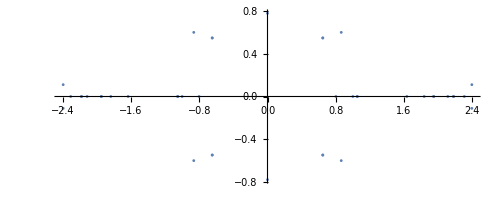

```mathematica
ComplexListPlot[w,ColorFunction->Hue,ImageSize->Full,PlotStyle->PointSize[0.005],PlotRange->All]
```

```mathematica
(* the anti-Desitter -Robertson-Walker -Jabobian -Lorentz model universe is Oval of Cassini shaped and 4 times larger and
is collapsing inward/ not expanding: Larger Hubble constants fron the Novas are small elliptical velocities*)
```

```mathematica
Abs[(2.39417996548432-0.11118064363156194 ⅈ)*c^2/(2*G)]/(4*10^27)
```

3.99974

```mathematica
tt=Tr[Tij]
```

-5.05952×10^59 (0.-(5.56325×10^-22 (1.-7.12844 r^2+1.88074 r^4+1. Cot[ϕ]^2-1. Csc[ϕ]^2))/r^2)-2.52976×10^59 (1. Cot[ϕ]^2+(0.5 Csc[ϕ]^2 (1.-7.12844 r^2+1.88074 r^4+1. Cot[ϕ]^2-1. Csc[ϕ]^2))/r^4+(5.31706+10.6341 r^2-18.9512 r^4+4. r^6+r^4 (5.31706-6.31706 r^2+1. r^4) Csc[ϕ]^2)/(r^4 (5.31706-6.31706 r^2+1. r^4)))-2.52976×10^59 (-((-1.+1.18807 r^2-0.188074 r^4) (1.-7.12844 r^2+1.88074 r^4+1. Cot[ϕ]^2-1. Csc[ϕ]^2))/(2 r^2)+(300.639-892.954 r^2+806.164 r^4-235.118 r^6+21.2683 r^8+(300.639-892.954 r^2+806.164 r^4-235.118 r^6+21.2683 r^8) Csc[ϕ]^2)/(r^4 (150.32-535.772 r^2+721.351 r^4-453.614 r^6+135.667 r^8-18.9512 r^10+1. r^12)))-2.52976×10^59 ((0.5 (1.-7.12844 r^2+1.88074 r^4+1. Cot[ϕ]^2-1. Csc[ϕ]^2))/r^4+(10.6341 r^2-18.9512 r^4+4. r^6+5.31706 Csc[ϕ]^2+r^4 (7.9756-9.4756 r^2+1.5 r^4+(2.65853-3.15853 r^2+0.5 r^4) Cos[2 ϕ]) Csc[ϕ]^4)/(r^4 (5.31706-6.31706 r^2+1. r^4)))

```mathematica
(*end*)
```